### Full Generality

```mathematica
α = ({{α1}, {α2}, {α3}});
c0=({{c01}, {A021}, {c03}}); (* A021 == c02 to satisfy the 0.5 constraint *)
c1=({{c11}, {c12}, {c13}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{0, 0, 0}, {A021, 0, 0}, {A031, A032, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0
-A021 h μ | 1 | 0
-A031 h μ | -A032 h μ | 1)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+(B021 I10 σ^2)/h
U+((B031+B032) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
U+A021 h U μ+(B021 I10 σ^2)/h
U+U (A031 h μ+A021 A032 h^2 μ^2)+((B031+B032) I10 σ^2)/h+A032 h μ (U+(B021 I10 σ^2)/h))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+I1 (β11+β12+β13) σ+(I10 (β21+β22+β23) σ)/h+h μ (U α1+α2 (U+A021 h U μ+(B021 I10 σ^2)/h)+α3 (U+U (A031 h μ+A021 A032 h^2 μ^2)+((B031+B032) I10 σ^2)/h+A032 h μ (U+(B021 I10 σ^2)/h)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 (U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2)+α3 (U+U (A031 h μ+A021 A032 h^2 μ^2)+1/2 (B031+B032) (W+Z/(√3)) σ^2+A032 h μ (U+1/2 B021 (W+Z/(√3)) σ^2)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (U α1+α2 (U+A021 h U μ)+α3 (U+A032 h U μ+U (A031 h μ+A021 A032 h^2 μ^2)))

1+h α1 μ+h α2 μ+h α3 μ+A021 h^2 α2 μ^2+A031 h^2 α3 μ^2+A032 h^2 α3 μ^2+A021 A032 h^3 α3 μ^3

```mathematica
stableeq = G/.  {μ -> z/h}
```

1+z α1+z α2+A021 z^2 α2+z α3+A031 z^2 α3+A032 z^2 α3+A021 A032 z^3 α3

```mathematica
TeXForm[1+z α1+z α2+A021 z^2 α2+z α3+A031 z^2 α3+A032 z^2 α3+A021 A032 z^3 α3]
```

\text{A021} \text{A032} \text{$\alpha $3} z^3+\text{A021}
   \text{$\alpha $2} z^2+\text{A031} \text{$\alpha $3}
   z^2+\text{A032} \text{$\alpha $3} z^2+\text{$\alpha $1}
   z+\text{$\alpha $2} z+\text{$\alpha $3} z+1

```mathematica
1+z Transpose[α].Inverse[K1].e /.  {μ -> z/h}
```

{{1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)}}

```mathematica
FullSimplify[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)]
```

1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3)

```mathematica
Solve[{1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3) == 1},z]
```

{{z→0},{z→(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3)},{z→(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3)}}

```mathematica
Solve[{1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3)== -1},z]
```

{{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)-(2^(1/3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))+1/(3 2^(1/3) A021 A032 α3)(-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)},{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)+((1+ⅈ √3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 2^(2/3) A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))-1/(6 2^(1/3) A021 A032 α3)(1-ⅈ √3) (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)},{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)+((1-ⅈ √3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 2^(2/3) A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))-1/(6 2^(1/3) A021 A032 α3)(1+ⅈ √3) (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)}}

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
vars = {α1,α2,α3,c01,c03,c11,c12,c13,β11,β12,β13,β21,β22,β23,A021,A031,A032,B021,B031,B032};
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
FindInstance[conds ,vars,Reals]
```

{α1+α2+α3==1,β11+β12+β13==1,β21+β22+β23==0,B021 α2+B031 α3+B032 α3==1,A021 α2+A031 α3+A032 α3==1/2,B021^2 α2+(B031+B032)^2 α3==3/2,c11 β11+c12 β12+c13 β13==1,c11 β21+c12 β22+c13 β23==-1}

{{α1→1/3,α2→0,α3→2/3,c01→8/5,c03→2,c11→-1,c12→0,c13→0,β11→-1,β12→0,β13→2,β21→1,β22→0,β23→-1,A021→0,A031→0,A032→3/4,B021→0,B031→0,B032→3/2}}

```mathematica
Minimize[{Min[(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],Min[(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],
Min[-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)-(2^(1/3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))+1/(3 2^(1/3) A021 A032 α3)(-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3),0],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8},vars,Reals]
```

$Aborted

```mathematica
Minimize[{Min[(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03},vars,Reals]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{α1→Indeterminate,α2→Indeterminate,α3→Indeterminate,c01→Indeterminate,c03→Indeterminate,c11→Indeterminate,c12→Indeterminate,c13→Indeterminate,β11→Indeterminate,β12→Indeterminate,β13→Indeterminate,β21→Indeterminate,β22→Indeterminate,β23→Indeterminate,A021→Indeterminate,A031→Indeterminate,A032→Indeterminate,B021→Indeterminate,B031→Indeterminate,B032→Indeterminate}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 > 0,c11>0},vars,Reals]
```

$Aborted

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1},vars,Reals]
```

{-4,{α1→13/4,α2→-7/2,α3→5/4,c01→0,c03→16/5,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→63/20,A032→1/20,B021→-1,B031→0,B032→-2}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 > 0},vars,Reals]
```

{-4,{α1→13/4,α2→-7/2,α3→5/4,c01→0,c03→16/5,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→63/20,A032→1/20,B021→-1,B031→0,B032→-2}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1,c03<1},vars,Reals]
```

{-4,{α1→13/4,α2→5/4,α3→-7/2,c01→0,c03→3/14,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→13/56,A032→-1/56,B021→-2,B031→0,B032→-1}}

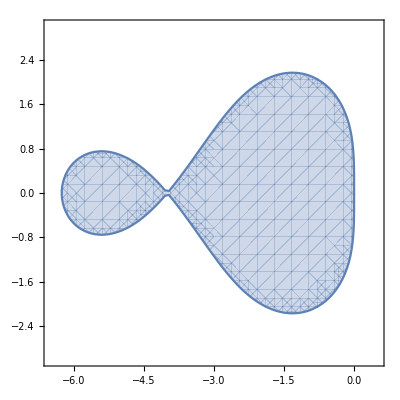

```mathematica
RegionPlot[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->13/56,A032->-1/56,α1->13/4,α2->5/4,α3->-7/2}]<1,{x,-6.5,0.5},{y,-3,3}]
```

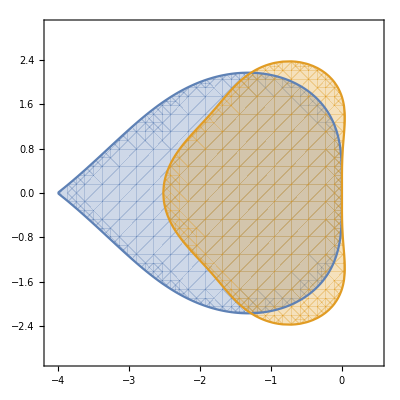

```mathematica
RegionPlot[{Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->63/20,A032->1/20,α1->13/4,α2->-7/2,α3->5/4}]<1,Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021-> 1,A031->1/4, A032-> 1/4,α1->1/6,α2->1/6,α3-> 2/3}]<1},{x,-4.1,0.5},{y,-3,3}]
```

```mathematica
NIntegrate[Boole[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->13/56,A032->-1/56,α1->13/4,α2->5/4,α3->-7/2}]<1],{x,-4.1,0.5},{y,-3,3}]
```

12.1215

```mathematica
NMaximize[{Chi[α1,α2,α3,A021,A031,A032],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1},vars,Reals]
```

$Aborted

```mathematica
Chi[A021_,A031_,A032_,α1_,α2_,α3_] :=N[(Total[Total[Boole[Table[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y}]<1,{x,-4,1,.02},{y,-3,3,.02}]]]]/75551)*(5*6)]
```

```mathematica
Chi[1,13/56,-1/56,13/4,5/4,-7/2]
```

12.0169

```mathematica
Chi[ 1,1/4, 1/4,1/6,1/6, 2/3]
```

9.08715

```mathematica
Total[Total[Table[1,{x,-4,1,.02},{y,-3,3,.02}]]]
```

75551

## Generate Constraint Functions for Julia Optimization

```mathematica
α = ({{a1}, {a2}, {a3}});
c0=({{c01}, {A021}, {c03}}); (* A021 == c02 to satisfy the 0.5 constraint *)
c1=({{c11}, {c12}, {c13}});
β1=({{b11}, {b12}, {b13}});
β2=({{b21}, {b22}, {b23}});
A0=({{0, 0, 0}, {A021, 0, 0}, {A031, A032, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
vars = {a1,a2,a3,c01,c03,c11,c12,c13,b11,b12,b13,b21,b22,b23,A021,A031,A032,B021,B031,B032};
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
```

{a1+a2+a3==1,b11+b12+b13==1,b21+b22+b23==0,a2 B021+a3 B031+a3 B032==1,A021 a2+A031 a3+A032 a3==1/2,a2 B021^2+a3 (B031+B032)^2==3/2,b11 c11+b12 c12+b13 c13==1,b21 c11+b22 c12+b23 c13==-1}

```mathematica
c02=A021;
a1=1-a2-a3;
b11=1-b12-b13;
b21=-b22-b23;
c03=A031+A032;
c12 = (-1-b21 c11-b23 c13)/b22;
b12 = (b22 (1-c11+b13 c11-b13 c13))/(-1+b23 c11-b23 c13);
```

```mathematica
conds = FullSimplify[{cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}]
```

{True,True,True,a2 B021+a3 (B031+B032)==1,2 A021 a2+2 (A031+A032) a3==1,2 a2 B021^2+2 a3 (B031+B032)^2==3,True,True}

```mathematica
Solve[{a2 B021+a3 (B031+B032)==1,2 A021 a2+2 (A031+A032) a3==1,2 a2 B021^2+2 a3 (B031+B032)^2==3},a2]
```

{}

```mathematica
D[a2*B021^2+a3*(B031+B032)^2-3/2,a3]
```

(B031+B032)^2

## Check Results From Julia

```mathematica
a2=-0.0814474211112128;
a3=0.4320323392388501;
c01=0.9124967304601606;
c11=1.8979474818325062;
c13=3.109002644776907;
b13=-0.7581247291175405;
b22=2.760896944565314;
b23=1.1274547344186254;
A021=0.19020779241797492;
A031=0.31939017555056765;
A032=0.8737888699715528;
B021=-1.6710925080964742;
B031=1.934645849904737;
B032=0.0649586850226064;
b12=-0.023557966826646754;
b11=1.7816826959441872;
b21=-3.8883516789839394;
c12=1.0411933455508264;
a1=0.6494150818723627;
c02=0.19020779241797492;
c03=1.1931790455221205;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
```

{0.,-1.11022×10^-16,2.22045×10^-16,-6.66134×10^-16,-8.32667×10^-16,-6.66134×10^-16,0.,0.}

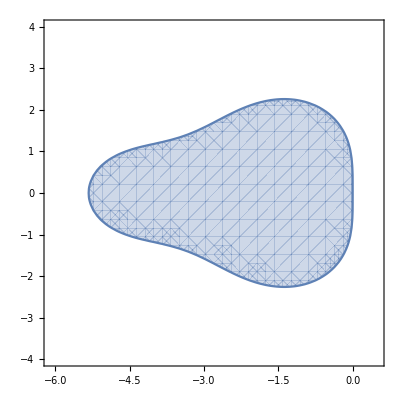

```mathematica
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

```mathematica
a2=-0.25138001688445977;
a3=0.0649868409305953;
c01=0.5723331064434696;
c11=0.9503978439140051;
c13=0.6056989999184046;
b13=2.006588631900022;
b22=1.3026770765487843;
b23=1.3405792021208602;
A021=-2.201363652967349;
A031=-0.32024578419138217;
A032=-0.5011333055965845;
B021=-2.2793103314361205;
B031=4.844616770085525;
B032=1.7263585886755126;
b12=-1.7951843452664449;
b11=0.7885957133664228;
b21=-2.6432562786696447;
c12=0.53747593991499;
a1=1.1863931759538644;
c02=-2.201363652967349;
c03=-0.8213790897879667;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
```

{-1.11022×10^-16,-2.22045×10^-16,-2.22045×10^-16,4.44089×10^-16,4.44089×10^-16,4.44089×10^-16,-4.44089×10^-16,0.}

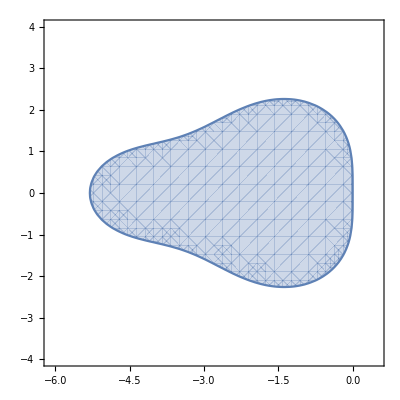

```mathematica
a2=1.0242748468969296;
a3=0.41081505799415324;
c01=0.025195823415196772;
c11=0.9220771747752234;
c13=0.023782353100744943;
b13=-0.11523634718338865;
b22=0.7142536179047427;
b23=0.5687633435651005;
A021=0.47106986354247526;
A031=-0.32995697693643955;
A032=0.37254301973571075;
B021=0.22303503873890748;
B031=1.0239670469580147;
B032=0.8541306635061033;
b12=0.03737643038474536;
b11=1.0778599167986433;
b21=-1.2830169614698432;
c12=0.23733043852217028;
a1=-0.43508990489108285;
c02=0.47106986354247526;
c03=0.042586042799271195;
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

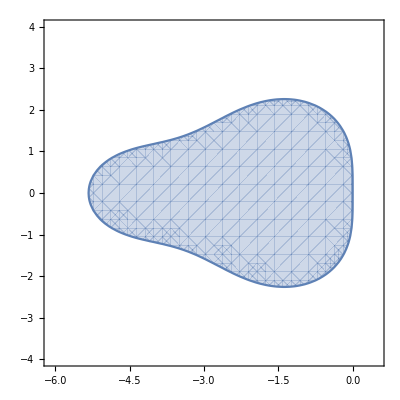

```mathematica
a2=1.29242545677646;
a3=-1.918880330520602;
c01=0.7417283312691364;
c11=0.8044227933059209;
c13=0.6176353482715539;
b13=4.352512452095754;
b22=2.3753488766419855;
b23=-0.5422723900310448;
A021=0.38686950754366095;
A031=0.09670857726100492;
A032=-0.09670857726100492;
B021=-4.305207443588581;
B031=-0.42405448268227675;
B032=-2.996773586891242;
b12=-2.1753678029150323;
b11=-1.1771446491807214;
b21=-1.8330764866109406;
c12=0.3407899833738219;
a1=1.626454873744142;
c02=0.38686950754366095;
c03=0.0;
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

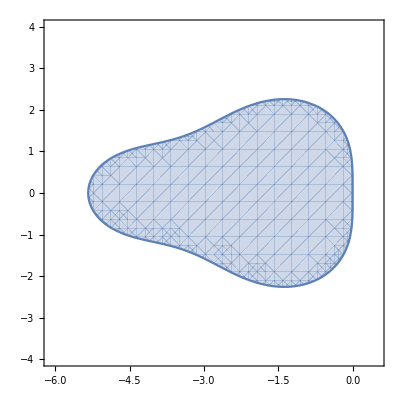

```mathematica
a2=1.5795481857236964;
a3=0.1659294015854011;
c01=0.12187122994699529;
c11=0.9702863765456154;
c13=0.8110368599589466;
b13=0.3990163408741854;
b22=4.106904757632921;
b23=0.4380437218528124;
A021=0.22469661067053365;
A031=-1.0485246706800526;
A032=1.9228777081203212;
B021=0.33669857376588846;
B031=1.3971078510550134;
B032=1.4243835434745178;
b12=-0.4117174116877337;
b11=1.0127010708135482;
b21=-4.5449484794857336;
c12=0.7437796022353017;
a1=-0.7454775873090975;
c02=0.22469661067053365;
c03=0.8743530374402686;
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

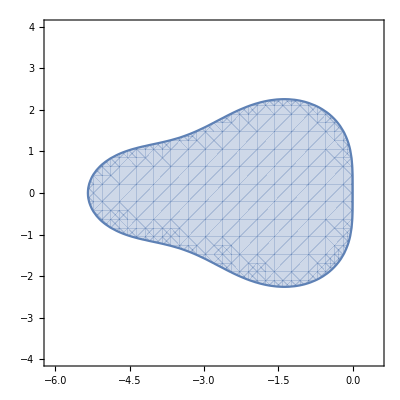

```mathematica
a2=0.5677553086597237;
a3=0.27958900151763677;
c01=0.9741307517466129;
c11=0.5544500741545535;
c13=0.3690586783313899;
b13=0.8632611357329213;
b22=4.021299791603951;
b23=0.7581710087408771;
A021=0.7421398107078702;
A031=-0.0638944838506604;
A032=0.3451866029110775;
B021=0.749018753541464;
B031=1.2972092789444352;
B032=0.758453223054547;
b12=-2.833541410317403;
b11=2.9702802745844816;
b21=-4.7794708003448285;
c12=0.34072772989877437;
a1=0.15265568982263955;
c02=0.7421398107078702;
c03=0.28129211906041707;
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## SOSRA, Integral = 16.818320893462346

```mathematica
a1=0.2889874966892885;
a2=0.6859880440839937;
a3=0.025024459226717772;
c01=0;
c02=0.6923962376159507;
c03=1;
c11=0;
c12=0.041248171110700504;
c13=1;
b11=-16.792534242221663;
b12=17.514995785380226;
b13=0.27753845684143835;
b21=0.4237535769069274;
b22=0.6010381474428539;
b23=-1.0247917243497813;
A021=0.6923962376159507;
A031=-3.1609142252828395;
A032=4.1609142252828395;
B021=1.3371632704399763;
B031=1.442371048468624;
B032=1.8632741501139225;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

{0.,8.88178×10^-16,0.,-1.11022×10^-16,0.,2.22045×10^-16,0.,0.}

-Graphics-

## Integral = 14.58381018021339

{0.,0.,0.,-8.49321×10^-13,-4.32987×10^-14,5.64659×10^-13,0.,0.}

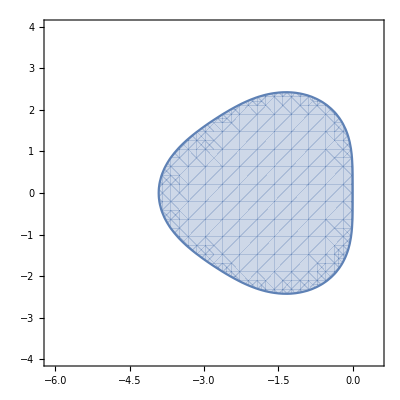

```mathematica
a1=0.26640748899442546;
a2=0.2500351293421496;
a3=0.4835573816634249;
c01=0;
c02=0.06576123275074512;
c03=1;
c11=0;
c12=0.5500213026098075;
c13=1;
b11=1.155014813827735;
b12=-2.566821097368929;
b13=2.411806283541194;
b21=1.224056341862874;
b22=-0.4979265533287831;
b23=-0.7261297885340909;
A021=0.06576123275074512;
A031=-2.0110265059940176;
A032=3.0110265059940176;
B021=0.7625188620735739;
B031=0.8920478212876166;
B032=0.7816801133592192;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## Integral = 16.452202222257842

{0.,-1.11022×10^-16,0.,2.22045×10^-16,0.,8.88178×10^-16,0.,0.}

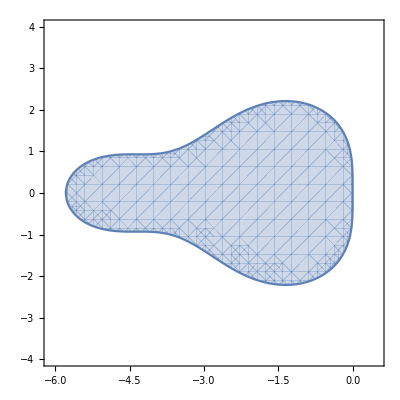

```mathematica
a1=0.171405185671326;
a2=0.5663296796561104;
a3=0.2622651346725636;
c01=0;
c02=0.4197817523386643;
c03=1;
c11=0;
c12=0.021851141069570413;
c13=1;
b11=-20.147399722421014;
b12=20.59747812255434;
b13=0.5499215998666748;
b21=-3.3396401777698297;
b22=4.436584614038265;
b23=-1.0969444362684357;
A021=0.4197817523386643;
A031=0.3931335301754404;
A032=0.6068664698245596;
B021=0.8021000435159605;
B031=0.6508309149067154;
B032=1.4300668757386774;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## Integral = 16.800967407003725

{0.,1.73195×10^-14,-2.22045×10^-16,-2.88547×10^-13,3.27738×10^-13,-3.03757×10^-13,0.,0.}

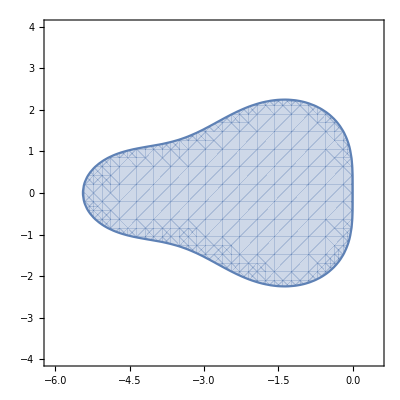

```mathematica
a1=0.2833573041619264;
a2=0.5337212838758844;
a3=0.18292141196218922;
c01=0;
c02=0.5940902070374888;
c03=1;
c11=0;
c12=0.0026858976547445407;
c13=1;
b11=400.33052764941846;
b12=-401.4086702554517;
b13=2.0781426060332424;
b21=-5.065890275600736;
b22=6.082226513529048;
b23=-1.0163362379283127;
A021=0.5940902070374888;
A031=0.35151033866285786;
A032=0.6484896613371421;
B021=1.619060925108918;
B031=0.6164129827996933;
B032=0.12637990798221393;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## Integral = 16.4533990144274

{-1.11022×10^-16,1.77636×10^-15,-4.44089×10^-16,6.66134×10^-16,1.11022×10^-16,6.43929×10^-15,0.,0.}

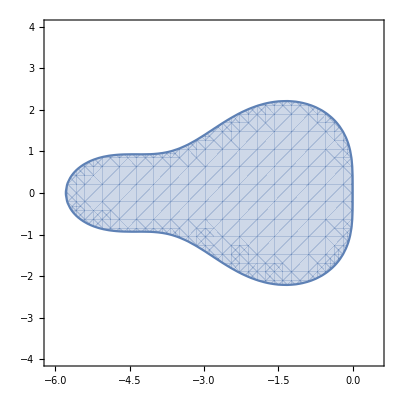

```mathematica
a1=0.4446523653656711;
a2=0.7191925152932691;
a3=-0.1638448806589402;
c01=0;
c02=0.9230419763034389;
c03=1;
c11=0;
c12=0.01569229790185835;
c13=1;
b11=-27.220376715860535;
b12=27.654336807319318;
b13=0.566039908541219;
b21=-5.419814753255972;
b22=6.522162469694742;
b23=-1.10234771643877;
A021=0.9230419763034389;
A031=1.44182877648547;
A032=-0.44182877648547003;
B021=2.151877769482312;
B031=2.570669570184941;
B032=0.7716038254518;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## SRADP, Integral = 12.252359301230095

{0.,2.22045×10^-16,0.,-3.07532×10^-14,2.33147×10^-15,2.07834×10^-13,0.,0.}

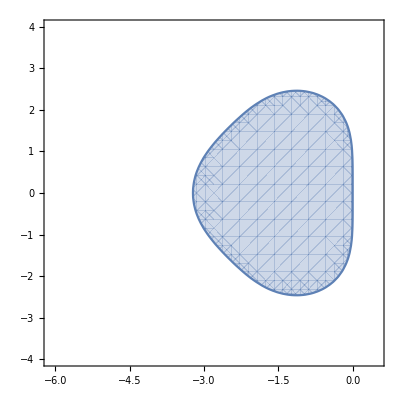

```mathematica
a1=0.5149274791532505;
a2=-0.0771620313703919;
a3=0.5622345522171415;
c01=0;
c02=0.8065437250919685;
c03=1;
c11=0;
c12=0.16393101191411438;
c13=1;
b11=-3.0303790492459295;
b12=3.6245562177634945;
b13=0.4058228314824352;
b21=-3.9707587938624584;
b22=5.945393101163363;
b23=-1.9746343073009047;
A021=0.8065437250919685;
A031=0.7386686884767767;
A032=0.2613313115232233;
B021=4.965883146452276;
B031=3.786654637383554;
B032=-1.3265112227290576;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

## SOSRA2, Integral = 16.818719824185532

{-1+α1+α2+α3+α4,-1+β11+β12+β13+β14,β21+β22+β23+β24,-1+0.76861 α2+1.18791 α3+B041 α4+B042 α4+B043 α4,-1/2+α2+1. α3+A041 α4+A042 α4+A043 α4,-3/2+0.590762 α2+1.41113 α3+(B041+B042+B043)^2 α4,{-1+β11,-1+β12,-1+β13,-1+β14},{1+β21,1+β22,1+β23,1+β24}}

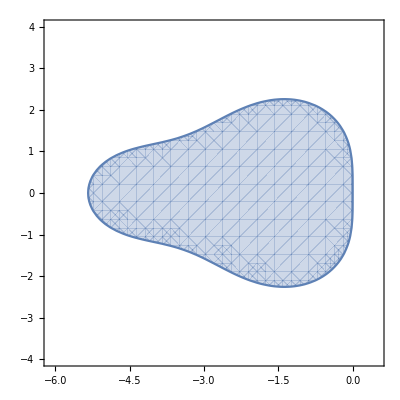

```mathematica
a1=0.4999999999999998;
a2=-0.9683897375354181;
a3=1.4683897375354185;
c01=0;
c02=1;
c03=1;
c11=0;
c12=1.0;
c13=1;
b11=0.0;
b12=0.92438032145683;
b13=0.07561967854316998;
b21=1.0;
b22=-0.8169981105823436;
b23=-0.18300188941765633;
A021=1;
A031=0.9511849235504364;
A032=0.04881507644956362;
B021=0.7686101171003622;
B031=0.43886792994934987;
B032=0.7490415909204886;
cond1 = First[First[Transpose[α].e]] -1;
cond2 = First[First[Transpose[β1].e]] - 1;
cond3 = First[First[Transpose[β2].e]] - 0;
cond4 = First[First[Transpose[α].B0.e]] - 1;
cond5 = First[First[Transpose[α].A0.e]] - 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] - 3/2;
cond7 = First[First[Transpose[β1].c1]] - 1;
cond8 = First[First[Transpose[β2].c1]] - -1;
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->A021,tA031->A031,tA032->A032,α1->a1,α2->a2,α3->a3}]<1},{x,-6.1,0.5},{y,-4,4}]
```

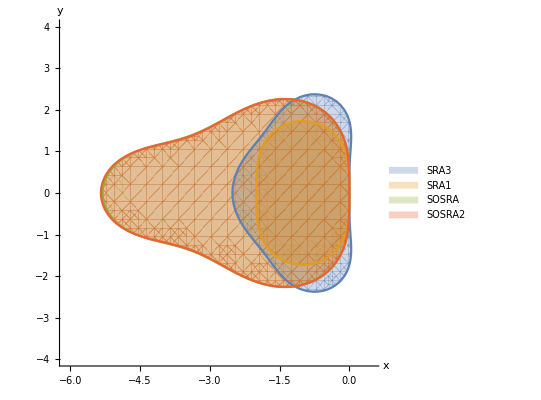

```mathematica
SetOptions[RegionPlot,BaseStyle->{FontFamily->"Ariel",FontSize->22}];
RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 1,tA031->1/4, tA032-> 1/4,α1->1/6,α2->1/6,α3-> 2/3}]<1,
Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 3/4,tA031->0, tA032-> 0,α1->1/3,α2->2/3,α3-> 0}]<1,
Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 0.6923962376159507,tA031->-3.1609142252828395, tA032-> 4.1609142252828395,α1->0.2889874966892885,α2->0.6859880440839937,α3-> 0.025024459226717772}]<1,
Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->1 ,tA031->0.9511849235504364, tA032-> 0.04881507644956362,α1->0.4999999999999998,α2->-0.9683897375354181,α3->1.4683897375354185}]<1},{x,-6.1,0.5},{y,-4,4},PlotLegends->{Style[SRA3,22],Style[SRA1,22],Style[SOSRA,22],Style[SOSRA2,22]},AxesLabel->Automatic,Axes->True,Frame->None]
```

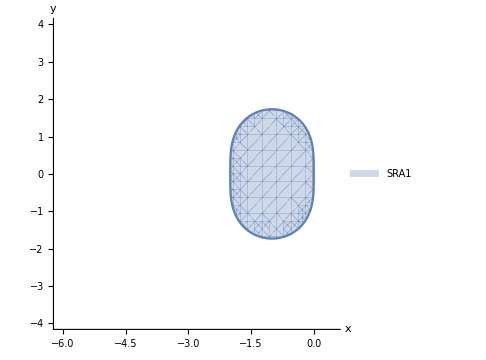
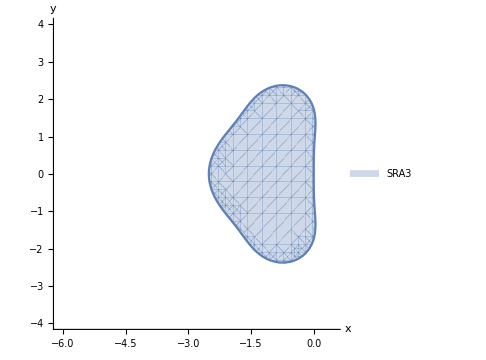
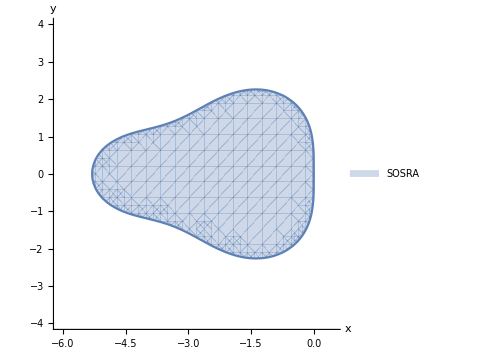
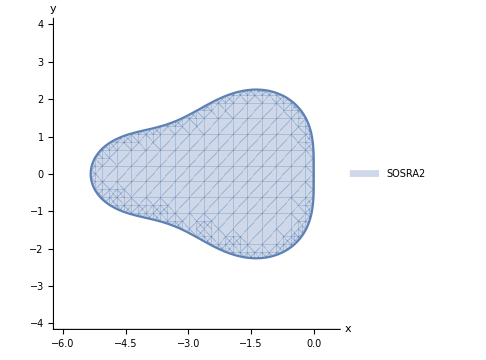
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetOptions[RegionPlot,BaseStyle->{FontFamily->"LM Roman 12",FontSize->22}];
p1 =RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 3/4,tA031->0, tA032-> 0,α1->1/3,α2->2/3,α3-> 0}]<1},{x,-6.1,0.5},{y,-4,4},PlotLegends->{Style[SRA1,22,FontFamily->"LM Roman 12"]},AxesLabel->Automatic,Axes->True,Frame->None,ImageSize->Medium];
p2 = RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 1,tA031->1/4, tA032-> 1/4,α1->1/6,α2->1/6,α3-> 2/3}]<1},{x,-6.1,0.5},{y,-4,4},PlotLabel->{Style[SRA3,22,FontFamily->"LM Roman 12"]},AxesLabel->Automatic,Axes->True,Frame->None,ImageSize->Medium];
p3 = RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021-> 0.6923962376159507,tA031->-3.1609142252828395, tA032-> 4.1609142252828395,α1->0.2889874966892885,α2->0.6859880440839937,α3-> 0.025024459226717772}]<1},{x,-6.1,0.5},{y,-4,4},PlotLegends->{Style[SOSRA,22,FontFamily->"LM Roman 12"]},AxesLabel->Automatic,Axes->True,Frame->None,ImageSize->Medium];
p4 = RegionPlot[{Abs[1+z (α1+α2+tA021 z α2+α3+tA032 z α3+(tA031 z+tA021 tA032 z^2) α3)/. {z-> x + ⅈ y,tA021->1 ,tA031->0.9511849235504364, tA032-> 0.04881507644956362,α1->0.4999999999999998,α2->-0.9683897375354181,α3->1.4683897375354185}]<1},{x,-6.1,0.5},{y,-4,4},PlotLegends->{Style[SOSRA2,22,FontFamily->"LM Roman 12"]},AxesLabel->Automatic,Axes->True,Frame->None,ImageSize->Medium];
Grid[{{p1,p2},{p3,p4}}]
```

```mathematica
Export["SOSRA_stability.pdf",%]
```

SOSRA_stability.pdf

```mathematica
Directory[]
```

D:\OneDrive\Computer\Documents